Dates and Times

In the Wolfram Language, Now gives your current date and time.

Get the current date and time (as of when I wrote this!):

```mathematica
Now
```

Wed 14 Sep 2022 08:12:54GMT-5

You can do computations on this, for example adding a week.

Add a week to the current date and time:

```mathematica
Now+LinguisticAssistant
```

Wed 21 Sep 2022 08:13:07GMT-5

Use ctrl= to enter a date in any standard format.

Enter a date:

```mathematica
LinguisticAssistant
```

Thu 23 Jun 1988

You can do arithmetic with dates, say, subtracting them to find how far apart they are.

Subtract two dates:

```mathematica
Now-LinguisticAssistant
```

12501. days

Convert the date difference to years:

```mathematica
UnitConvert[Now-LinguisticAssistant,"Years"]
```

34.2493 yr

DayRange is the analog of Range for dates:

Give a list of the days spanning from yesterday to tomorrow:

```mathematica
DayRange[Yesterday,Tomorrow]
```

{Tue 13 Sep 2022,Wed 14 Sep 2022,Thu 15 Sep 2022}

DayName finds the day of the week for a particular date.

Compute the day of the week 45 days from now:

```mathematica
DayName[Today+LinguisticAssistant]
```

Saturday

Once you know a date, there are lots of things you can compute. For example, MoonPhase gives the phase of the moon (or, more accurately, the fraction of the Moon that is illuminated when seen from the Earth).

Compute the phase of the moon now:

```mathematica
MoonPhase[Now]
```

0.808

Compute the phase of the moon on a certain date:

```mathematica
MoonPhase[LinguisticAssistant]
```

0.5756

Generate an icon for the phase of the moon:

```mathematica
MoonPhase[LinguisticAssistant,"Icon"]
```

-Graphics-

If you know both the date and a location on Earth, you can work out when the sun will rise and set.

Compute when sunset will be today at my current location:

```mathematica
Sunset[Here,Today]
```

Minute: Tue 13 Sep 2022 19:05GMT-5

Compute the time between successive sunrises:

```mathematica
Sunrise[Here,Tomorrow]-Sunrise[Here,Today]
```

1441 min

They’re about a minute off from being exactly 1 day (24 hours) apart:

```mathematica
Sunrise[Here,Tomorrow]-Sunrise[Here,Today]-LinguisticAssistant
```

1 min

Time zones are one of many subtleties. LocalTime gives the time in the time zone of a particular location.

Find the local time now in New York City:

```mathematica
LocalTime[LinguisticAssistant]
```

Wed 14 Sep 2022 09:17:02GMT-4

Find the local time now in London:

```mathematica
LocalTime[LinguisticAssistant]
```

Wed 14 Sep 2022 14:17:11GMT+1

Just as the Wolfram Language has built-in knowledge about notable geographic locations, so also it has built in knowledge about notable historical events.

Find the date of the Apollo 11 moon landing:

```mathematica
DateObject[]
```

Minute: Sun 20 Jul 1969 20:17GMT

Among the many areas where the Wolfram Language has extensive data is weather. The function AirTemperatureData uses this data to give the historical air temperature at a particular time and place.

Find the air temperature here at 6 pm yesterday:

```mathematica
AirTemperatureData[Here,LinguisticAssistant]
```

66. °F

If you provide a pair of dates, AirTemperatureData computes a time series of estimated temperatures between those dates.

Give a time series of air temperature measurements from a week ago until now:

```mathematica
AirTemperatureData[Here,{LinguisticAssistant,Now}]
```

TimeSeries[…]

You can use ListPlot and ListLinePlot to plot values in a time series.

Plot the list of air temperature measurements:

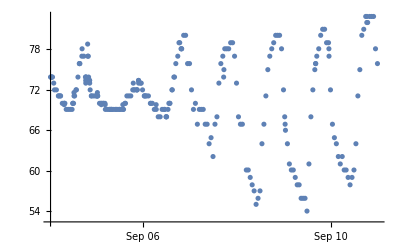

```mathematica
ListPlot[AirTemperatureData[Here,{LinguisticAssistant,Now}]]
```

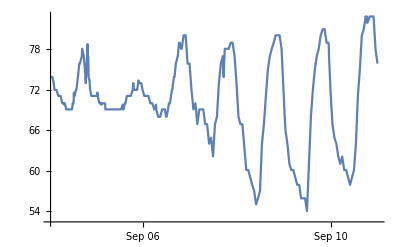

```mathematica
ListLinePlot[AirTemperatureData[Here,{LinguisticAssistant,Now}]]
```

The plot shows that, not surprisingly, the temperature is higher during the day than at night.

As another example, let’s look at data that goes much further back in time. WordFrequencyData tells one how frequently a particular word occurs, say in a sample of books published in a given year. There’s a lot of history one can see by looking at how this changes over the years and centuries.

Find the time series of how frequently the word “automobile” occurs:

```mathematica
WordFrequencyData["automobile","TimeSeries"]
```

TimeSeries[…]

Cars started to exist around 1900, but gradually stopped being called “automobiles”:

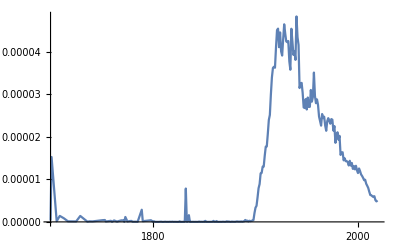

```mathematica
ListLinePlot[WordFrequencyData["automobile","TimeSeries"]]
```

WordFrequencyData is set up to make it easy to compare frequencies of different words. Let’s see how “monarchy” and “democracy” have fared over the years. “Democracy” is definitely more popular now, but “monarchy” was more popular in the 1700s and 1800s.

Compare historical word frequency between “monarchy” and “democracy”:

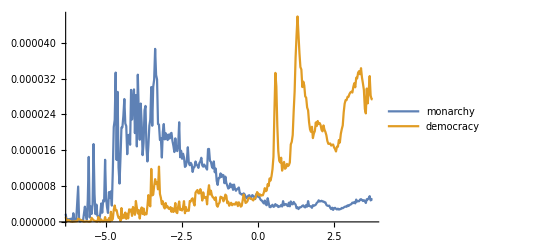

```mathematica
ListLinePlot[WordFrequencyData[{"monarchy","democracy"},"TimeSeries"]]
```

The Wolfram Language has lots of historical real-world data. If you ask directly for something like the population of a country, it’ll give you the latest estimate it has. But you can use Dated to have it give you historical values.

The latest estimate of the population of the USA:

```mathematica
["Population"]
```

331449281 people

An estimate of the population in the year 2000:

```mathematica
[Dated["Population",2000]]
```

281710914 people

A time series of population for all dates where it’s known:

```mathematica
[Dated["Population",All]]
```

TimeSeries[…]

Plot the population over time:

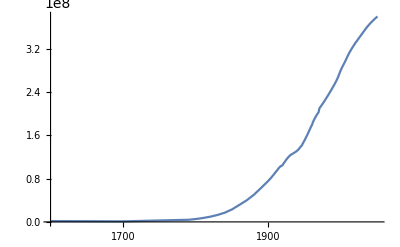

```mathematica
ListLinePlot[[Dated["Population",All]]]
```

Vocabulary

Now |   | current date and time 
Today |   | date object for today 
Tomorrow |   | date object for tomorrow 
Yesterday |   | date object for yesterday 
DayRange[date_1,date_2] |   | list of dates from date_1to date_2 
DayName[date] |   | day of the week of date
MoonPhase[date] |   | moon phase on date
Sunrise[location,date] |   | time of sunrise on date at location 
Sunset[location,date] |   | time of sunset on date at location   
LocalTime[location] |   | current time at location  
AirTemperatureData[location,time] |   | air temperature at date at  location   
AirTemperatureData[location,{time_1,time_2}] |   | time series of air temperatures from
time_1 to time_2 at location 
ListPlot[timeseries], ListLinePlot[timeseries] |   | plot time series 
WordFrequencyData["word","TimeSeries"] |   | time series of word frequencies
entity[Dated["property",year]] |   | value of a property in a certain year
entity[Dated["property",All]] |   | time series of values of a property

"15 Exercises Available"
"with 7 extras" | "Get Started »"

Compute how many days have elapsed since January 1, 1900. »

| Sample expected output: |  
  | 44816. "days" |

Compute what day of the week January 1, 2000 was. »

| Sample expected output: |  
  | Saturday |

Find the date a hundred thousand days ago. »

| Sample expected output: |  
  | "Fri 29 Nov 1748" |

Find the local time in Delhi. »

| Sample expected output: |  
  | "Wed 14 Sep 2022 19:00:32""GMT"+5.5 |

Find the length of daylight today by subtracting today’s sunrise from today’s sunset. »

| Sample expected output: |  
  | 753 "min" |

Generate an icon for the current phase of the moon. »

| Sample expected output: |  
  |  |

Make a list of the numerical phase of the moon for each of the next 10 days. »

| Sample expected output: |  
  | {0.7529,0.6628,0.5684,0.4731,0.3796,0.2904,0.2084,0.1361,0.07637,0.03229} |

Generate a list of icons for the moon phases from tomorrow until 10 days from now. »

| Sample expected output: |  
  | {,,,,,,,,,} |

Compute the time today between sunrise in London and in New York City. »

| Sample expected output: |  
  | 304 "min" |

Find the number of years from the Apollo 11 moon landing until now. »

| Sample expected output: |  
  | 53.1883 "yr" |

Find the air temperature at the Eiffel Tower at noon yesterday. »

| Sample expected output: |  
  | 77. "°F" |

Plot the temperature at the Eiffel Tower over the past week. »

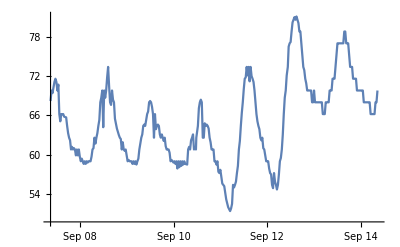
| Sample expected output: |  
  | -Graphics- |

Find the difference in air temperatures between Los Angeles and New York City now. »

| Expected output: |  
  | 1.1 "°F" |

Plot the historical frequency of the word “groovy”. »

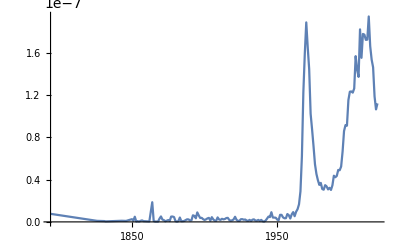
| Expected output: |  
  | -Graphics- |

Find the difference in population of the UK between 2000 and 1900. »

| Expected output: |  
  | 20948151 "people" |

Compute how many weeks have elapsed since January 1, 1900. »

| Expected output: |  
  | 6402.29 "wk" |

Compute the time between 3 pm today and sunset today. »

| Expected output: |  
  | 4 "h" |

Generate an icon of the phase of the moon on August 29, 1959. »

| Expected output: |  
  |  |

Make a line plot of the numerical phase of the moon for each of the next 30 days. »

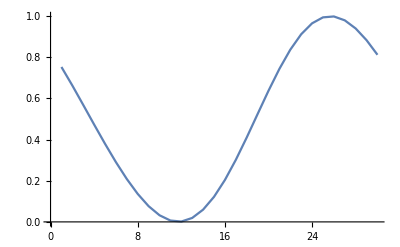
| Expected output: |  
  | -Graphics- |

Make a Manipulate of the icon for the moon phase over the next 15 days. »

Show in a column the times of sunrise for 10 days, starting today. »

| Expected output: |  
  | "Minute: ""Wed 14 Sep 2022 06:33""GMT"-5
"Minute: ""Thu 15 Sep 2022 06:34""GMT"-5
"Minute: ""Fri 16 Sep 2022 06:35""GMT"-5
"Minute: ""Sat 17 Sep 2022 06:36""GMT"-5
"Minute: ""Sun 18 Sep 2022 06:37""GMT"-5
"Minute: ""Mon 19 Sep 2022 06:38""GMT"-5
"Minute: ""Tue 20 Sep 2022 06:39""GMT"-5
"Minute: ""Wed 21 Sep 2022 06:40""GMT"-5
"Minute: ""Thu 22 Sep 2022 06:41""GMT"-5
"Minute: ""Fri 23 Sep 2022 06:42""GMT"-5 |

Plot together the historical frequencies of the words “science” and “technology”. »

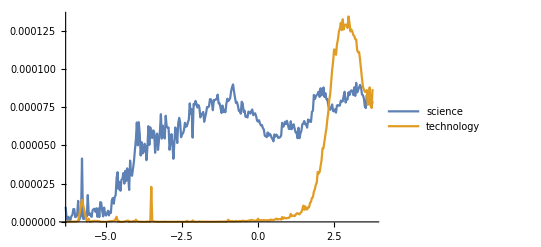
| Expected output: |  
  | -Graphics- |

Q&A

How can I get a date as a string?

Use DateString[date]. There are many options for the format of the string. For example, DateString[date,"DateShort"] uses short day and month names.

How can I extract the month or some other element from a date?

Use DateValue. DateValue[date,"Month"] gives the month number, DateValue[date,"MonthName"] gives the month name, etc.

How far in the past can dates be in the Wolfram Language?

As far as you want. The Wolfram Language knows about historical calendar systems, and the history of time zones. It also has the data to accurately compute sunrise, etc. going back at least 1000 years.

Why are sunrise and sunset given only to the minute?

Because you can’t compute more accurately than that exactly when the sun will actually rise and set without knowing things like air temperature that affect the bending of light in the Earth’s atmosphere.

Where does the Wolfram Language get air temperature data from?

The worldwide network of weather stations, located at airports and other places. If you’ve got your own air temperature measuring device, you can connect it to the Wolfram Language through the Wolfram Data Drop (see Section 43).

What is a time series?

It’s a way of specifying the values of something at a series of times. You can enter a time series in the Wolfram Language as TimeSeries[{{time_1,value_1},{time_2,value_2}, ...}]. The Wolfram Language lets you do arithmetic and many other operations with time series.

How do ListPlot and ListLinePlot work with time series?

They plot values against times or dates. The values can be given in a TimeSeries[...] or in a list of the form {{time_1,value_1},{time_2,value_2}, ...}.

What types of historical information does the Wolfram Language have?

Lots of detailed data about things like countries (populations, GDPs, ..) and companies (stock prices, ...), as well as about things from earthquakes to airplane flights. It also has information on military conflicts, as well as on when things were built, discovered, founded, etc.

Tech Notes

The Wolfram Language decides whether to interpret a date like 8/10/15 as month/day/year or day/month/year based on what country you’re in. You can pick the other interpretation if you want.

Monday, etc. are symbols with intrinsic meaning, not strings.

DateObject lets you specify the “granularity” of a date (day, week, month, year, decade, etc.). CurrentDate, NextDate, DateWithinQ, etc. operate on granular dates.

You can see what’s “inside” DateObject[...] using InputForm.

More to Explore

Guide to Dates & Times in the Wolfram Language »